# Notebook 2 : Performing Sequence Analysis with Mathematica

The aim of this lab notebook is to give users the ideas of how to perform sequence analysis using Mathematica so that they can further develop relevant skills (e.g., writing more complicated searching function) in their future research.

Note: The prerequsite knowledge about DNA structure can be found at : http://www.blc.arizona.edu/Molecular_Graphics/DNA_Structure/DNA_Tutorial.HTML
and the prerequsite knowledge about mRNA, amino acids and genetic code can be found at :  http://users.rcn.com/jkimball.ma.ultranet/BiologyPages/C/Codons.html

## 1. Using the StringReplace and StringReverse function

Consider the following string which we call nucstring

```mathematica
nucstring="acCtagGgCCTTAcga"
```

acCtagGgCCTTAcga

The function StringReplace allows us to replace/modify characters in a string. The syntax for StringReplace can be found using the help menu (StringReplace). In this example we want to replace the string characters "t" and "g" with their upper case counterpart

```mathematica
StringReplace[nucstring,{"t"->"T","g"->"G"}]
```

acCTaGGGCCTTAcGa

In Mathematica the construct exp1→ exp2 (where exp1 stands for any Mathematica expression) represents a replacement rule. Note that in the second argument in StringReplace is a replacement rule or a list of replacement rules. In this case the replacement rule involves strings e,g. "t"→"T" etc.

Let us expand on this example by first defining a new string which is a replicates  our original string. We call the new string nucstring2

```mathematica
nucstring2="acCtagGgCCTTAcgaacCtagGgCCTTAcga"
```

acCtagGgCCTTAcgaacCtagGgCCTTAcga

The following example shows that StringReplace searches through the complete string and makes replacements whenever there is a match.

```mathematica
StringReplace[nucstring2,{"tag"->"BGH"}]
```

acCBGHGgCCTTAcgaacCBGHGgCCTTAcga

If we are given a string we can reverse the order of the string using StringReverse function. Here is an example using our nucstring

```mathematica
{nucstring, StringReverse[nucstring]}
```

{acCtagGgCCTTAcga,agcATTCCgGgatCca}

One application of StringReverse is to explore properties of the  complement of a DNA sequence of bases. This is done in Example 2

### Example 1: Create RNA from DNA sequence using StringReplace

Consider the following DNA sequence taken from a FASTA file, where the letters "a","g","c","t" represent the bases in DNA

```mathematica
myDNA="agatggcggcgctgaggggtcttgggggctctaggccggccacctactggtttgcagcggagacgacgcatggggcctgcgcaataggagtacgctgcctgggaggcgtgactagaagcggaagtagttgtgggcgcctttgcaaccgcctgggacgccgccgagtggtctgtgcaggttcgcgggtcgctggcgggggtcgtgagggagtgcgccgggagcggagatatggagggagatggttcagacccagagcctccagatgccggggaggacagcaagtccgagaatggggagaatgcgcccatctactgcatctgccgcaaaccggacatcaactgcttcatgatcgggtgtgacaactgcaatgagtggttccatggggactgcatccggatcactgagaagatggccaaggccatccgggagtggtactgtcgggagtgcagagagaaagaccccaagctagagattcgctatcggcacaagaagtcacgggagcgggatggcaatgagcgggacagcagtgagccccgggatgagggtggagggcgcaagaggcctgtccctgatccagacctgcagcgccgggcagggtcagggacaggggttggggccatgcttgctcggggctctgcttcgccccacaaatcctctccgcagcccttggtggccacacccagccagcatcaccagcagcagcagcagcagatcaaacggtcagcccgcatgtgtggtgagtgtgaggcatgtcggcgcactgaggactgtggtcactgtgatttctgtcgggacatgaagaagttcgggggccccaacaagatccggcagaagtgccggctgcgccagtgccagctgcgggcccgggaatcgtacaagtacttcccttcctcgctctcaccagtgacgccctcagagtccctgccaaggccccgccggccactgcccacccaacagcagccacagccatcacagaagttagggcgcatccgtgaagatgagggggcagtggcgtcatcaacagtcaaggagcctcctgaggctacagccacacctgagccactctcagatgaggaccta";
```

To generate RNA from this sequence we need to replace  every occurrence of the character "t" with  the charter "u". We can use StringReplace to do this operation

```mathematica
myRNA=StringReplace[myDNA,"t"->"u"]
```

agauggcggcgcugaggggucuugggggcucuaggccggccaccuacugguuugcagcggagacgacgcauggggccugcgcaauaggaguacgcugccugggaggcgugacuagaagcggaaguaguugugggcgccuuugcaaccgccugggacgccgccgaguggucugugcagguucgcgggucgcuggcgggggucgugagggagugcgccgggagcggagauauggagggagaugguucagacccagagccuccagaugccggggaggacagcaaguccgagaauggggagaaugcgcccaucuacugcaucugccgcaaaccggacaucaacugcuucaugaucgggugugacaacugcaaugagugguuccauggggacugcauccggaucacugagaagauggccaaggccauccgggagugguacugucgggagugcagagagaaagaccccaagcuagagauucgcuaucggcacaagaagucacgggagcgggauggcaaugagcgggacagcagugagccccgggaugaggguggagggcgcaagaggccugucccugauccagaccugcagcgccgggcagggucagggacagggguuggggccaugcuugcucggggcucugcuucgccccacaaauccucuccgcagcccuugguggccacacccagccagcaucaccagcagcagcagcagcagaucaaacggucagcccgcauguguggugagugugaggcaugucggcgcacugaggacuguggucacugugauuucugucgggacaugaagaaguucgggggccccaacaagauccggcagaagugccggcugcgccagugccagcugcgggcccgggaaucguacaaguacuucccuuccucgcucucaccagugacgcccucagagucccugccaaggccccgccggccacugcccacccaacagcagccacagccaucacagaaguuagggcgcauccgugaagaugagggggcaguggcgucaucaacagucaaggagccuccugaggcuacagccacaccugagccacucucagaugaggaccua

## 2. Some basic functions for manipulating strings

In this section we introduce the reader to a few new functions that are useful for manipulation strings. If we are given a string and we want to break it down into a list of individual characters we can use the function Characters. Consider our previous example string called nucstring. Here are the individual characters of nucstring

```mathematica
myListofChar=Characters[nucstring]
```

{a,c,C,t,a,g,G,g,C,C,T,T,A,c,g,a}

We now have a list of individual characters that we used to create nucstring. We can reverse the process with the function StringJoin

```mathematica
StringJoin[myListofChar]
```

acCtagGgCCTTAcga

Mathematica has numerous functions for manipulating lists. We will examine a few of them. Consider the function Partition This function allows one to partition a list into sublists with various degrees of overlap of the partitions. The following link describes the syntax for using the partition function ( Partition ). Here is a simple example that partitions our list of characters into sublist of three characters with no overlap of partitions

```mathematica
mySublist1=Partition[myListofChar,3]
```

{{a,c,C},{t,a,g},{G,g,C},{C,T,T},{A,c,g}}

Here is a partition in which the sublists are offset by one character

```mathematica
mySublist2=Partition[myListofChar,3,1]
```

{{a,c,C},{c,C,t},{C,t,a},{t,a,g},{a,g,G},{g,G,g},{G,g,C},{g,C,C},{C,C,T},{C,T,T},{T,T,A},{T,A,c},{A,c,g},{c,g,a}}

Suppose now we want to convert all the sublists into a unified string. We can devise a replacement rule that will do this operation that makes use of the function StringJoin

```mathematica
mySublist1/.{x_,y_,z_}:>StringJoin[x,y,z]
```

{acC,tag,GgC,CTT,Acg}

The above statement contains several new notations: The operator /. is the shorthand for ReplaceAll function and is used with replacement rules; the notation {x_,y_,z_} defines a named pattern; and the notation :> is a delayed rule which means the RHS of the rule is not evaluated until the replacement is done. An alternative way of doing the same task is to use the Map function

```mathematica
Map[StringJoin[#]&,mySublist1]
```

{acC,tag,GgC,CTT,Acg}

In this example the function StringJoin is mapped onto each sublist; the symbol # denotes the slot function and is used with a pure Function . During the Map operation the contents of each sublist is substituted into the slot.

We can also use the Apply  function. In this operation the Head of each sublist which is List is replaced with StringJoin. See the previous links for an explanation of the syntax for using  Map and Apply; also check the ECH198 Introduction to Mathematica for more details an examples using this functions)

```mathematica
Apply[StringJoin,mySublist1,2]
```

{acC,tag,GgC,CTT,Acg}

This example illustrates that there are often several ways to do a task in Mathematica. The choice of method is usually one of  convenience, i.e. use the method the method you are most comfortable with. There are times, however , where the method of choice is based on computational efficiency.

### Example 2: Translating Codons to Amino Acids

In this example we use our DNA string to create a sequence of amino acids. First we construct a set of rules for the codons. For the meaning of these rules, please see http://molbio.info.nih.gov/molbio/gcode.html 
and http://users.rcn.com/jkimball.ma.ultranet/BiologyPages/C/Codons.html

```mathematica
CodonRules={"tca"->"S","tcc"->"S","tcg"->"S","tct"->"S","ttc"->"F",   "ttt"->"F","tta"->"L","ttg"->"L","tac"->"Y","tat"->"Y","taa"->"_","tag"->"_","tgc"->"C","tgt"->"C","tga"->"_","tgg"->"W","cta"->"L","ctc"->"L","ctg"->"L","ctt"->"L","cca"->"P","ccc"->"P","ccg"->"P","cct"->"P","cac"->"H","cat"->"H","caa"->"Q","cag"->"Q","cga"->"R","cgc"->"R","cgg"->"R","cgt"->"R","ata"->"I","att"->"I","atc"->"I","atg"->"M","aca"->"T","acc"->"T","acg"->"T","act"->"T","aac"->"N","aat"->"N","aaa"->"K","aag"->"K","agc"->"S","agt"->"S","aga"->"R","agg"->"R","gta"->"V","gtc"->"V","gtg"->"V","gtt"->"V","gca"->"A","gcc"->"A","gcg"->"A","gct"->"A","gac"->"D","gat"->"D","gaa"->"E","gag"->"E","gga"->"G","ggc"->"G","ggg"->"G","ggt"->"G"}
```

{tca→S,tcc→S,tcg→S,tct→S,ttc→F,ttt→F,tta→L,ttg→L,tac→Y,tat→Y,taa→_,tag→_,tgc→C,tgt→C,tga→_,tgg→W,cta→L,ctc→L,ctg→L,ctt→L,cca→P,ccc→P,ccg→P,cct→P,cac→H,cat→H,caa→Q,cag→Q,cga→R,cgc→R,cgg→R,cgt→R,ata→I,att→I,atc→I,atg→M,aca→T,acc→T,acg→T,act→T,aac→N,aat→N,aaa→K,aag→K,agc→S,agt→S,aga→R,agg→R,gta→V,gtc→V,gtg→V,gtt→V,gca→A,gcc→A,gcg→A,gct→A,gac→D,gat→D,gaa→E,gag→E,gga→G,ggc→G,ggg→G,ggt→G}

Note here we will operate directly on the DNA sample rather than first converting it to RNA as done in Example 1. The codon rules use "t" rather than "u". In order to apply the codon replacement rules, we first transform our DNA sequence into a list of characters using the Characters function and then Partition the list into sublists containing three amino acids.

```mathematica
Partition[Characters[myDNA],3]/.{x_,y_,z_}:>StringJoin[x,y,z]
```

{aga,tgg,cgg,cgc,tga,ggg,gtc,ttg,ggg,gct,cta,ggc,cgg,cca,cct,act,ggt,ttg,cag,cgg,aga,cga,cgc,atg,ggg,cct,gcg,caa,tag,gag,tac,gct,gcc,tgg,gag,gcg,tga,cta,gaa,gcg,gaa,gta,gtt,gtg,ggc,gcc,ttt,gca,acc,gcc,tgg,gac,gcc,gcc,gag,tgg,tct,gtg,cag,gtt,cgc,ggg,tcg,ctg,gcg,ggg,gtc,gtg,agg,gag,tgc,gcc,ggg,agc,gga,gat,atg,gag,gga,gat,ggt,tca,gac,cca,gag,cct,cca,gat,gcc,ggg,gag,gac,agc,aag,tcc,gag,aat,ggg,gag,aat,gcg,ccc,atc,tac,tgc,atc,tgc,cgc,aaa,ccg,gac,atc,aac,tgc,ttc,atg,atc,ggg,tgt,gac,aac,tgc,aat,gag,tgg,ttc,cat,ggg,gac,tgc,atc,cgg,atc,act,gag,aag,atg,gcc,aag,gcc,atc,cgg,gag,tgg,tac,tgt,cgg,gag,tgc,aga,gag,aaa,gac,ccc,aag,cta,gag,att,cgc,tat,cgg,cac,aag,aag,tca,cgg,gag,cgg,gat,ggc,aat,gag,cgg,gac,agc,agt,gag,ccc,cgg,gat,gag,ggt,gga,ggg,cgc,aag,agg,cct,gtc,cct,gat,cca,gac,ctg,cag,cgc,cgg,gca,ggg,tca,ggg,aca,ggg,gtt,ggg,gcc,atg,ctt,gct,cgg,ggc,tct,gct,tcg,ccc,cac,aaa,tcc,tct,ccg,cag,ccc,ttg,gtg,gcc,aca,ccc,agc,cag,cat,cac,cag,cag,cag,cag,cag,cag,atc,aaa,cgg,tca,gcc,cgc,atg,tgt,ggt,gag,tgt,gag,gca,tgt,cgg,cgc,act,gag,gac,tgt,ggt,cac,tgt,gat,ttc,tgt,cgg,gac,atg,aag,aag,ttc,ggg,ggc,ccc,aac,aag,atc,cgg,cag,aag,tgc,cgg,ctg,cgc,cag,tgc,cag,ctg,cgg,gcc,cgg,gaa,tcg,tac,aag,tac,ttc,cct,tcc,tcg,ctc,tca,cca,gtg,acg,ccc,tca,gag,tcc,ctg,cca,agg,ccc,cgc,cgg,cca,ctg,ccc,acc,caa,cag,cag,cca,cag,cca,tca,cag,aag,tta,ggg,cgc,atc,cgt,gaa,gat,gag,ggg,gca,gtg,gcg,tca,tca,aca,gtc,aag,gag,cct,cct,gag,gct,aca,gcc,aca,cct,gag,cca,ctc,tca,gat,gag,gac,cta}

We can then apply the list of codonRules and then wrap the expression with StringJoin

```mathematica
StringJoin[Partition[Characters[myDNA],3]/.{x_,y_,z_}:>StringJoin[x,y,z]/.CodonRules]
```

RWRR_GVLGALGRPPTGLQRRRRMGPAQ_EYAAWEA_LEAEVVVGAFATAWDAAEWSVQVRGSLAGVVRECAGSGDMEGDGSDPEPPDAGEDSKSENGENAPIYCICRKPDINCFMIGCDNCNEWFHGDCIRITEKMAKAIREWYCRECREKDPKLEIRYRHKKSRERDGNERDSSEPRDEGGGRKRPVPDPDLQRRAGSGTGVGAMLARGSASPHKSSPQPLVATPSQHHQQQQQQIKRSARMCGECEACRRTEDCGHCDFCRDMKKFGGPNKIRQKCRLRQCQLRARESYKYFPSSLSPVTPSESLPRPRRPLPTQQQPQPSQKLGRIREDEGAVASSTVKEPPEATATPEPLSDEDL

## 3. Counting bases in a sequence

Suppose we are given a sequence and we would like to determine the occurrence frequency of a particular base. We can readily do this calculation using the function Select. Select takes a list as its first argument and then returns elements in that list that match a given criterion. Let us consider a simple example. Suppose we are given the list "attcgta" and we want to determine the number of times the base "t" occurs. Our strategy is to first convert the string into a list of characters using Characters, then select out the character "t" using the criterion defined as a pure function  (#=="t")&. The number of occurrences is then determined with the function Length which gives the length of the list returned by Select. Let us see how this works

```mathematica
Select[Characters["attcgta"],(#=="t")&]
```

{t,t,t}

If we wrap the above expression with length we get the number of occurrences of the base"t"

```mathematica
Length[Select[Characters["attcgta"],(#=="t")&]]
```

3

We can use these ideas to construct a simple function that does the desired task

```mathematica
numOfOcc[sequence_String,base_String]:=Length[Select[Characters[sequence],(#==base)&]]
```

Let us apply this function to our DNA sequence used earlier to determine the number of occurrences of the base "a"

```mathematica
numOfOcc[myDNA,"a"]
```

230

### Example 3: Frequency distribution of bases in a sequence

In this example we consider a DNA sequence and then determine the frequency distribution of the bases in the sequence. We will make use of the graphical tools in the Graphics`Graphics` package. To use these tools we need to load the package. This is done with the following command

```mathematica
<<Graphics`Graphics`;
```

General::obspkg: "Graphics`Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Next we will make use of our function numOfOcc to determine the frequency of the bases in our DNA sequence. We will make this function onto a list of the 4 bases. This generates the number of occurrences for the individual bases.

```mathematica
Map[numOfOcc[myDNA,#]&,{"a","t","c","g"}]
```

{230,175,302,373}

To show these results graphically , we can use a Bar Chart. The first argument is the list of occurrences

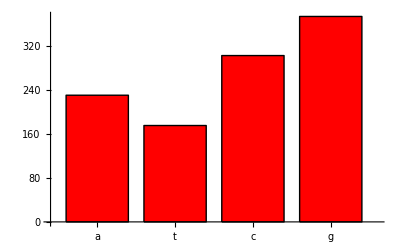

```mathematica
BarChart[Map[numOfOcc[myDNA,#]&,{"a","t","c","g"}],BarLabels->{"a","t","c","g"}]
```

If we wanted, we could make a function that generates a graphical representation for given DNA sequence. In this example we make use of the Module function to construct a self-contained function that generates a bar chart for a DNA sequence:

```mathematica
seqBarChart[sequence_String]:=Module[{base},
Get["Graphics`Graphics`"];
numOfOcc[base_]:=Length[Select[Characters[sequence],(#==base)&]];BarChart[Map[numOfOcc[#]&,{"a","t","c","g"}],BarLabels->{"a","t","c","g"}]];
```

To use this function we simply supply the DNA sequence (it must be a string) as an argument. There are many ways to embellish this plot ,but for simplicity I have given the bare essentials.

```mathematica
seqBarChart[myDNA]
```

General::obspkg: "Graphics`Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

-Graphics-

## 4. More functions for manipulating strings

If we are given a sequence that contains both upper case letters and lower case letters , there is a simple function that can convert the sequence to a desired  form. The functions are ToUpperCase and ToLowerCase . Let's demonstrate how these functions work on our string nucstring

```mathematica
{ToUpperCase[nucstring],ToLowerCase[nucstring]}
```

{ACCTAGGGCCTTACGA,acctagggccttacga}

Note that these functions are Listable. That is, they can be thread over lists of Characters as shown below

```mathematica
ToUpperCase[Characters[nucstring]]
```

{A,C,C,T,A,G,G,G,C,C,T,T,A,C,G,A}

Suppose we want to determine the positions of a particular character in a string. The appropriate function is called StringPosition. The first argument of StringPosition is the string under investigation, the second argument is the sublist you are seeking. Here is an example for the character "a in nucstring. The output is a list of sublists that give the starting and end position of the sublist

```mathematica
StringPosition[nucstring,"a"]
```

{{1,1},{5,5},{16,16}}

Since our sublist is a single character, the output is a sublist with identical indices. If we want the beginning position we can  Map the function First onto each sublist

```mathematica
Map[First[#]&,StringPosition[nucstring,"a"]]
```

{1,5,16}

Alternatively, we can Flatten all sublists and then use Union to pick out the common elements

```mathematica
Union[Flatten[StringPosition[nucstring,"a"]]]
```

{1,5,16}

We can also devise a replacement rule to do the task:

```mathematica
StringPosition[nucstring,"a"]/.{x_,y_}->x
```

{1,5,16}

The last three examples illustrate once again that Mathematica allows one to solve the problem in  a variety of ways.

Suppose we want to remove improper characters from a sequence. If we know the location we can use the function StringDrop to accomplish the task. Consider our protein sequence

```mathematica
proteinString="CLKJLDiCXLklJDMXLKJdLmxLEIKXMDLKJcMDLKJXMeNNlB"
```

CLKJLDiCXLklJDMXLKJdLmxLEIKXMDLKJcMDLKJXMeNNlB

Let us assume that the improper characters are

```mathematica
improperChar={"B","J","N","O","U","b","j","n","o","u"};
```

We can use StringPosition to find their location. Since any given character may appear more than once in the string, we need to flatten the sublists at level 1. This gives then the positions for the rogue characters

```mathematica
loc=Flatten[Map[StringPosition[proteinString,#]&,improperChar],1]
```

{{46,46},{4,4},{13,13},{19,19},{33,33},{39,39},{43,43},{44,44}}

Then we can use StringReplacePart, using and empty character as the second argument.

```mathematica
StringReplacePart[proteinString,"",loc]
```

CLKLDiCXLklDMXLKdLmxLEIKXMDLKcMDLKXMel

We can insert "gaps into the sequence by using a Null character

```mathematica
StringReplacePart[proteinString," ",loc]
```

CLK LDiCXLkl DMXLK dLmxLEIKXMDLK cMDLK XMe  l

For comparison, here is the original protein sequence

```mathematica
proteinString
```

CLKJLDiCXLklJDMXLKJdLmxLEIKXMDLKJcMDLKJXMeNNlB

### Example 4 : Application of ToUpperCase

In this example we have a string consisting of UpperCase and LowerCase characters. We would like to reverse the character case: change UpperCase to LowerCase and LowerCase to UpperCase. Here is the string

```mathematica
myString="VRNrIAelslrrFMVALILdIKrTPgNKPriacmICDIDtYIvEa"
```

VRNrIAelslrrFMVALILdIKrTPgNKPriacmICDIDtYIvEa

If we attempt to use the function ToUpperCase, then we lose all reference to what were the initial LowerCase characters

```mathematica
myStringUC=ToUpperCase[myString]
```

VRNRIAELSLRRFMVALILDIKRTPGNKPRIACMICDIDTYIVEA

One way to avoid this problem is to define a set of replacement rules and then use the StringReplace function. The function CharacterRange defines a sequence of characters. Thus all the UpperCase characters in the alphabet are

```mathematica
CharacterRange["A","Z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

Likewise the LowerCase characters are

```mathematica
CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Here is a rule that replaces UpperCase characters with LowerCase characters. We have made use of the function Thread to construct the sequence of rules.

```mathematica
UCtoLCRule=Thread[CharacterRange["A","Z"]->CharacterRange["a","z"]]
```

{A→a,B→b,C→c,D→d,E→e,F→f,G→g,H→h,I→i,J→j,K→k,L→l,M→m,N→n,O→o,P→p,Q→q,R→r,S→s,T→t,U→u,V→v,W→w,X→x,Y→y,Z→z}

Here is a similar rule that does the reverse

```mathematica
LCtoUCRule=Thread[CharacterRange["a","z"]->CharacterRange["A","Z"]]
```

{a→A,b→B,c→C,d→D,e→E,f→F,g→G,h→H,i→I,j→J,k→K,l→L,m→M,n→N,o→O,p→P,q→Q,r→R,s→S,t→T,u→U,v→V,w→W,x→X,y→Y,z→Z}

Next we use the StringReplace function and as the second argument we Join the two sets of rules:

```mathematica
StringReplace[myString,Join[UCtoLCRule,LCtoUCRule]]
```

vrnRiaELSLRRfmvalilDikRtpGnkpRIACMicdidTyiVeA

If we compare with the original string it is clear we have achieved the desired result.

```mathematica
myString
```

VRNrIAelslrrFMVALILdIKrTPgNKPriacmICDIDtYIvEa

## 5. Generating a random nucleotide

Consider the following set of bases

```mathematica
bases={"a","c","g","t"};
```

We can use Random to generate a random integer between 1 and 4 as follows

```mathematica
Random[Integer,{1,4}]
```

2

Then we use the Part ([[]] function to extract a base from a base list

```mathematica
bases[[Random[Integer,{1,4}]]]
```

t

Suppose we want a sequence with 10 bases. We use Table to generate 10 random copies, Please review the syntax we used for Table to generate copies.

```mathematica
Table[bases[[Random[Integer,{1,4}]]],{10}]
```

{t,g,t,c,c,t,c,c,c,c}

If we wrap the above with StringJoin we have our sequence

```mathematica
StringJoin[Table[bases[[Random[Integer,{1,4}]]],{10}]]
```

accccactca

Finally, we can construct a function (using the above expression) that takes an integer as an argument. Note that the variable n is pattern matched and our function will only work if the input is an integer.

```mathematica
randomDNA[n_Integer]:=StringJoin[Table[bases[[Random[Integer,{1,4}]]],{n}]]
```

Let us test out our function by generating a sequence with 50 randomly selected bases

```mathematica
randomDNA[50]
```

agtcattagggcgcttcacggaaacgtagataaaaccgattagaaagtct

### Example 5: Statistics on DNA sequences

In this section we consider a set of DNA sequences and then ask how do these sequences differ from each other, and then quantify that difference. Let us first generate a set of random DNA sequences using our previous function. The sequences will be called DNAsequence[i], i=1,2,…4

```mathematica
bases={"a","c","g","t"};randomDNA[n_Integer]:=StringJoin[Table[bases[[Random[Integer,{1,4}]]],{n}]]
```

```mathematica
Table[DNAsequence[i]=randomDNA[20],{i,1,4}]
```

{gtgtcattgatctgagaact,cagtccttgtacgagttagt,cgcggacattggccagtgtc,caatacgatgagtcctacgt}

We can readily pick out an base from a given sequence using StringTake

```mathematica
StringTake[DNAsequence[1],{1,1}]
```

g

To determine the number of bases at a given position that are equal in a given pair of DNA sequences, we use Table to loop through all possible positions and use an If statement to check for equality. If two bases at the same position are equal we update our count variable. Here is the code that compares DNAsequence[1] with DNAsequence[4]

```mathematica
count=0;Table[If[StringTake[DNAsequence[1],{j,j}]==StringTake[DNAsequence[4],{j,j}],count++,0],{j,1,StringLength[DNAsequence[1]]}];
count
```

4

Now let us write a function that does the same task but also reports on some statistics. The function has two arguments: the number of DNA sequences and the length of the sequence ( all sequences have equal length). The sequences are generated at random and the first sequences is compared with all other sequences. The function returns the average fraction of positions that are the same between two sequences in a set of n sequences.

```mathematica
DNACompare[numberOfSequences_,lengthOfSequence_]:=Module[{bases,randomDNA,DNAsequence,count},bases={"a","c","g","t"};randomDNA[n_Integer]:=StringJoin[Table[bases[[Random[Integer,{1,4}]]],{n}]];
Table[DNAsequence[i]=randomDNA[lengthOfSequence],{i,1,numberOfSequences}];
Table[count[p]=0,{p,2,numberOfSequences}];
Table[Table[If[StringTake[DNAsequence[1],{j,j}]==StringTake[DNAsequence[p],{j,j}],count[p]++,0],{j,1,StringLength[DNAsequence[1]]}],{p,2,numberOfSequences}];
average=N[(Apply[Plus,Table[count[p],{p,2,numberOfSequences}]]/(numberOfSequences-1))/lengthOfSequence]]
```

Here is the result for 20 sequences each with 20 bases.

```mathematica
DNACompare[20,20]
```

0.218421

## 6. Generating cartoons of DNA strands

We show in this section how to generate a DNA strand that shows the base pairing. A simple way to do this is to use a GridBox. Suppose we had the DNA sequence "c a a g t" and we want to show its pairing with the complementary bases "g t t c a". Here is  a graphical way of doing it. Make use of CellPrint, Cell,  RowBox, and GridBox

```mathematica
CellPrint[Cell[RowBox[{GridBox[{{"c","a","a","g","t"},Table["|",{5}],{"g","t","t","c","a"}},GridBaseline->Bottom]}],"Output"]]
```

c | a | a | g | t
| | | | | | | | |
g | t | t | c | a

Here is a simpler method that makes use of DisplayForm and GridBox

```mathematica
DisplayForm[GridBox[{{"c","a","a","g","t"},Table["|",{5}],{"g","t","t","c","a"}},GridBaseline->Bottom]]
```

c | a | a | g | t
| | | | | | | | |
g | t | t | c | a

Here is a function that takes an integer as its argument Length of the DNA strand and then generates the corresponding DNA strand,

```mathematica
DNAstrand[x_]:=Module[{bases,randomDNA,complementRule,sequence2},bases={"a","c","g","t"};randomDNA[n_Integer]:=StringJoin[Table[bases[[Random[Integer,{1,4}]]],{n}]];sequence=randomDNA[x];
complementRule={"a"->"t","t"->"a","g"->"c","c"->"g"};
sequence2=StringReplace[sequence,complementRule];
DisplayForm[GridBox[{Characters[sequence],Table["|",{x}],Characters[sequence2]},GridBaseline->Bottom]]]
```

Here is an example

```mathematica
DNAstrand[30]
```

a | c | c | t | t | a | g | a | c | t | a | c | c | g | c | t | c | c | g | t | g | a | t | a | c | t | g | t | a | a
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
t | g | g | a | a | t | c | t | g | a | t | g | g | c | g | a | g | g | c | a | c | t | a | t | g | a | c | a | t | t

One difficulty with this method is that as the DNA sequence gets longer, the DNA cartoon does not wrap on the page. Thus we need a more general method for creating a cartoon. The following method was suggested by David Park of the Mathgroup. In this example we use symbols instead of strings for the bases. The function makes use of several functions which are described below

First we generate a random nucliotide using the Switch function.  The advantage of the using the Switch function is that we can specify more general statistics for the distribution of bases. The function is given below where the bases have equal probability

```mathematica
randomnucl:=Switch[Random[],_?(#<0.25&),a,_?(#<0.5&),t,_?(#<0.75&),c,_,g]
```

We can now use Table to generate the bases in the nucliotide chain. Here is a chain with 10 bases

```mathematica
mydata=Table[randomnucl,{10}]
```

{c,a,t,c,c,t,t,t,t,t}

Note that in the above function we are working with symbols not strings! We will also need a function called basepair that swops that bases to generate the DNA sequence

```mathematica
basepair[n_]:=Switch[n,a,t,t,a,c,g,g,c,_,""]
```

We can then map this function onto mydata to generate the complementary bases

```mathematica
Map[basepair,mydata]
```

{g,t,a,g,g,a,a,a,a,a}

To generate a cartoon of the paired bases we can proceed as follows. We use the function ToBoxes function but this is not needed as shown later

```mathematica
DisplayForm[ GridBox[{Map[ToBoxes,mydata], Table["|", {Length[mydata]}],
           Map[ ToBoxes ,Map[basepair,mydata]]}, GridBaseline -> Bottom]]
```

c | a | t | c | c | t | t | t | t | t
| | | | | | | | | | | | | | | | | | |
g | t | a | g | g | a | a | a | a | a

Note this will also work without using the ToBoxes function

```mathematica
DisplayForm[ GridBox[{mydata, Table["|", {Length[mydata]}],
           Map[basepair,mydata]}, GridBaseline -> Bottom]]
```

c | a | t | c | c | t | t | t | t | t
| | | | | | | | | | | | | | | | | | |
g | t | a | g | g | a | a | a | a | a

We will need to display a sequences that wrap on the page. This can be done by using GridBoxes as follows. Here is a single cartoon

```mathematica
sub1= GridBox[{mydata, Table["|", {Length[mydata]}],
           Map[basepair,mydata]}, GridBaseline -> Bottom];
```

If we take this DNA cartoon and use it in Gridboxes as follows, we get a stacking of DNA cartoons

```mathematica
DisplayForm[FrameBox[GridBox[{{sub1},{sub1}},RowLines -> True]]]
```

c | a | t | c | c | t | t | t | t | t
| | | | | | | | | | | | | | | | | | |
g | t | a | g | g | a | a | a | a | a
c | a | t | c | c | t | t | t | t | t
| | | | | | | | | | | | | | | | | | |
g | t | a | g | g | a | a | a | a | a

These ideas are included in the the folloing function which generates the display of the sequence. The function takes several arguments: The first argument defines the length of the DNA sequence; the second argument, called start, defines where in the sequence we want to start displaying; the third argument is the length of the row (i.e the number of base pairs displayed in a row); the third argument is the number of rows.

```mathematica
DNAstrand2[x_,start_,rowlength_,rows_]:=Module[{randomnucl,basepair,data,subdata, rowgrid},
randomnucl:=Switch[Random[],_?(#<0.25&),a,_?(#<0.5&),t,_?(#<0.75&),c,_,g];
data=Table[randomnucl,{x}];
basepair[n_]:=Switch[n,a,t,t,a,c,g,g,c,_,""];
    rowgrid[subdata_] :=
      GridBox[{Map[ToBoxes,subdata], Table["|", {rowlength}],
            Map[ToBoxes ,Map[basepair, subdata]]}, GridBaseline -> Bottom];
    subdata =
      Take[data, {start, Min[start + rows rowlength - 1, Length[data]]}];
    subdata = Partition[subdata, rowlength, rowlength, {1, 1}, " "];
    subdata =Map[ {rowgrid[#]} & ,subdata];
    DisplayForm[FrameBox[GridBox[subdata, RowLines -> True]]]]
```

Let us illustrate how this function works

```mathematica
DNAstrand2[200,5,30,6]
```

a | g | t | g | a | a | g | c | g | a | t | c | c | t | g | a | t | a | t | g | a | g | g | c | g | g | c | g | g | g
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
t | c | a | c | t | t | c | g | c | t | a | g | g | a | c | t | a | t | a | c | t | c | c | g | c | c | g | c | c | c
g | t | g | g | t | g | t | t | c | c | g | t | t | c | g | t | t | g | g | t | g | a | a | c | a | c | a | g | c | g
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
c | a | c | c | a | c | a | a | g | g | c | a | a | g | c | a | a | c | c | a | c | t | t | g | t | g | t | c | g | c
g | t | g | t | g | a | c | g | g | c | a | g | a | t | t | g | a | c | t | a | a | g | g | a | a | t | g | c | t | a
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
c | a | c | a | c | t | g | c | c | g | t | c | t | a | a | c | t | g | a | t | t | c | c | t | t | a | c | g | a | t
t | g | t | t | a | a | a | a | g | a | a | c | t | a | a | c | c | g | g | t | g | t | t | a | t | t | a | c | t | t
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
a | c | a | a | t | t | t | t | c | t | t | g | a | t | t | g | g | c | c | a | c | a | a | t | a | a | t | g | a | a
g | t | t | a | c | g | g | g | c | a | t | g | g | g | t | c | t | c | a | t | t | g | c | a | c | c | t | g | g | c
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
c | a | a | t | g | c | c | c | g | t | a | c | c | c | a | g | a | g | t | a | a | c | g | t | g | g | a | c | c | g
t | a | a | c | g | a | t | c | c | t | a | a | c | a | c | a | g | a | a | c | c | a | t | g | t | a | a | t | t | g
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
a | t | t | g | c | t | a | g | g | a | t | t | g | t | g | t | c | t | t | g | g | t | a | c | a | t | t | a | a | c

## 7. Adding color to sequences

Suppose we had a string and we wanted to print it in the notebook  with a specified color . We can use the StyleForm wrapper, and then specify the FontColor option, as shown below

```mathematica
myString=StyleForm["abcdefg",FontColor->RGBColor[0,0,1]]
```

abcdefg

Another way of doing this is at the cell level using a StyleBox

```mathematica
CellPrint[Cell[BoxData[StyleBox["abcdefg",FontColor->RGBColor[0,0,1]]],"Output"]]
```

abcdefg

Now if we have a string and we want to color certain characters (say the UpperCase characters), we can proceed as follows. For each UpperCase character we add a StyleBox with the appropriate FontColor option. Consider the following string

```mathematica
myString="abFGec"
```

abFGec

Next we devise a rule that adds the color info to the UpperCase characters. We first break up the string into its individual characters, and then use our replacement rule

```mathematica
Characters[myString]/.x_String?UpperCaseQ:>StyleBox[x,FontColor->RGBColor[1,0,0]]
```

{a,b,StyleBox[F,FontColor→RGBColor[1,0,0]],StyleBox[G,FontColor→RGBColor[1,0,0]],e,c}

We then wrap this output with RowBox, BoxData, Cell, and CellPrint

```mathematica
CellPrint[Cell[BoxData[RowBox[Characters[myString]/.x_String?UpperCaseQ:>StyleBox[x,FontColor->RGBColor[1,0,0]]]],"Output"]]
```

abFGec

We see that the characters are spaced apart. If instead of RowBox we use GridBox then we can use the ColumnSpacings option to close up the characters, as shown below

```mathematica
CellPrint[Cell[BoxData[GridBox[{Characters[myString]/.x_String?UpperCaseQ:>StyleBox[x,FontColor->RGBColor[1,0,0]]},ColumnSpacings->0]],"Output"]]
```

a | b | F | G | e | c

Let us use our randomDNA function to generate a sequence and then mutate it and show the mutation as red characters. Here is our randomDNA function

```mathematica
bases={"a","c","g","t"};randomDNA[n_Integer]:=StringJoin[Table[bases[[Random[Integer,{1,4}]]],{n}]]
```

```mathematica
myDNA=randomDNA[50]
```

caatttacttcgtgccaacagctttgccggaaagtaggttagatgtcttg

The function that mutates our DNA strand is  shown below. The function that colors the characters that are mutated is called colorfunc. Note since we are tagging the mutated bases in red we can forgo using UpperCase to identify the changes

```mathematica
mutateDNA3[sequence_,numberOfMutations_]:=Module[{bases,selectBaseForMutation,x,tempString,mutatedSequence,i,candPosForMutation,mutatePosition,mutatePositionFlag,mutatedBase,colorfunc},
colorfunc[p_]:=CellPrint[Cell[BoxData[GridBox[{Characters[p]/.x_String?UpperCaseQ:>StyleBox[ToLowerCase[x],FontColor->RGBColor[1,0,0]]},ColumnSpacings->0]],"Output"]];
bases={"a","c","g","t"};selectBaseForMutation:=ToUpperCase[bases[[Random[Integer,{1,4}]]]];
tempString=sequence;
i=1;
While[i<numberOfMutations+1,candPosForMutation=StringPosition[tempString,bases]/.{x_?IntegerQ,y_?IntegerQ}->x;
mutatePosition=Random[Integer,{1,StringLength[sequence]}];
mutatePositionFlag=Length[Intersection[candPosForMutation,{mutatePosition}]];
mutatedBase=selectBaseForMutation;
mutatedSequence=If[mutatePositionFlag==1&&ToUpperCase[StringTake[tempString,{x,x}/.x->mutatePosition]]!=mutatedBase,i=i+1;StringReplacePart[tempString,mutatedBase,{x,x}/.x->mutatePosition],tempString];tempString=mutatedSequence];mutatedSequence;colorfunc[mutatedSequence]]
```

Let us apply the mutation to our sequence

```mathematica
mutateDNA3[myDNA,20]
```

c | t | a | t | a | g | a | c | t | t | t | g | t | g | c | t | a | g | g | t | a | g | c | g | t | g | c | c | g | g | a | c | g | g | c | c | g | a | t | t | a | t | a | t | c | t | a | t | t | g

Compare this with the original sequence

```mathematica
myDNA
```

caatttacttcgtgccaacagctttgccggaaagtaggttagatgtcttg

## 8. Pattern Searching in Strings

Suppose we are given a string and we want to determine whether the string contains a certain string pattern or " motif". Consider the following simple example:

```mathematica
mystring1="MNIDDKLETVELFLKCGGIDEMQSSRTQESEMRQQDMISHDELMVHEETVKNDEEQMETHERLPQ"
```

MNIDDKLETVELFLKCGGIDEMQSSRTQESEMRQQDMISHDELMVHEETVKNDEEQMETHERLPQ

Now suppose we are interested in determining whether the motif "MRQ" exists in the string. We can use the StringMatchQ function. If a  match is found then StringMatchQ returns True, otherwise it returns False

```mathematica
StringMatchQ[mystring1,"*MRQ*"]
```

True

We can determine the location of this motif using the  StringPosition function

```mathematica
StringPosition[mystring1,"MRQ"]
```

{{32,34}}

In this example the motif appeared only once. Suppose we look for the motif "ETV"

```mathematica
StringPosition[mystring1,"ETV"]
```

{{8,10},{48,50}}

In this case the motif appears twice.  We can write our own function to determine the number of occurrences of our motif.

```mathematica
numOccMotif[str_String,motif_String]:=Length[StringPosition[str,motif]]
```

```mathematica
numOccMotif[mystring1,"ETV"]
```

2

Sometimes it is convenient to know the beginning string position of the motif. In the above example this occurred at  positions 8 and 48. We can write a simple function that does the task:

```mathematica
positionOfMotif[str_String,motif_String]:=Map[First[#]&,StringPosition[str,motif]]
```

```mathematica
positionOfMotif[mystring1,"ETV"]
```

{8,48}

In biology one normally is interested in determining whether short segments of DNA or protein exist in the parent structure. These motifs are rarely a fixed structure, as discussed in the examples above. More often the motif is of variable length and in certain locations the base or amino acid is of no importance, or belongs to a certain class. Thus the search procedures we used in the above example are of not applicable .

## 9. Reading in the PDB file into Mathematica

In this section we are going to investigate how we can use Mathematica to manipulate GenBank (Genetic Sequence Data Bank) files. The data bank can be found at the following URL:
				http://www.ncbi.nlm.nih.gov/Genbank/index.html
Our first task is to download a GenBank file. For this purpose we are going to work with the file for the Homo Sapiens mRNA for AIRE Protein.. The nucleotide ID for  file is Z97990. Use the above link to connect to the web site and then paste in the nucleotide ID given above into the query box. Select "Nucleotide" in the Search box  Click on "Go".  The web page should then have  a link Z97990 that gives details of the  file. Open that data file and try to obtain a text copy file of the data.  Save your file to an appropriate folder on your computer. You can name it anything you like but for the purpose of this tutorial I will be referring to the file as "Z97990.txt".

We are going to make use of the ReadList function. The first argument to ReadList is the PATH to your file, expressed as a String. A convenient way of obtaining the PATH to your file is to use the FileBrowse function which is located in the Experimental context. When evaluated, the FileBrowse function generates a browse window on your desktop which you can use to find your data file that you downloaded from the PDB web site. The second argument of ReadList is the type of objects you want to read. For our purposes Word will suffice. For later manipulations we want to break up the data file as a sequence of lines, such that each line of the file is considered a record and represented as a String. We can achieve this by using the WordSeparators function and select the appropriate separator for your file. In most cases this will be "\r" or "\n" which represent  a carriage return or new line character. Since the file is quite large we will suppress the output using the ";" command . More details on how to use ReadList can be found by clicking on ReadList . To see the complete file remove the ";" at the end of the following statement:

```mathematica
myGenBankfile=ReadList[Experimental`FileBrowse[False],Word, WordSeparators->{"\r"}];
```

Experimental`FileBrowse::obs: Experimental`FileBrowse has been superseded by SystemDialogInput, and is now obsolete. It will not be included in future versions of Mathematica.

Here is what the first 10 lines of the file look like

```mathematica
Table[myGenBankfile[[i]],{i,1,10}]//TableForm
```

LOCUS       HSAPECED                2245 bp    mRNA    linear   PRI 18-APR-2005
DEFINITION  Homo Sapiens mRNA for AIRE protein.
ACCESSION   Z97990
VERSION     Z97990.1  GI:2665370
KEYWORDS    Aire protein.
SOURCE      Homo sapiens (human)
  ORGANISM  Homo sapiens
            Eukaryota; Metazoa; Chordata; Craniata; Vertebrata; Euteleostomi;
            Mammalia; Eutheria; Euarchontoglires; Primates; Catarrhini;
            Hominidae; Homo.

In the above output we have a LOCUS, DEFINITION, ACCESSION, etc record types. But there are also lines without a record type, e.g. the line containing the string

		"Eukaryota; Metazoa; Chordata; Craniata; Vertebrata; Euteleostomi;"

Note also that each record of the file is a string with lots of white space.

```mathematica
myGenBankfile[[1]]//FullForm
```

"LOCUS       HSAPECED                2245 bp    mRNA    linear   PRI 18-APR-2005"

The number of records in this file can be determined using the Length function

```mathematica
Length[myGenBankfile]
```

111

If we look at the full file structure and we are interested in getting the DNA sequence data, we see it is not possible to select the DNA rows from this list by record type as the DNA rows have no record type

```mathematica
myGenBankfile
```

{LOCUS       HSAPECED                2245 bp    mRNA    linear   PRI 18-APR-2005,DEFINITION  Homo Sapiens mRNA for AIRE protein.,ACCESSION   Z97990,VERSION     Z97990.1  GI:2665370,KEYWORDS    Aire protein.,SOURCE      Homo sapiens (human),  ORGANISM  Homo sapiens,            Eukaryota; Metazoa; Chordata; Craniata; Vertebrata; Euteleostomi;,            Mammalia; Eutheria; Euarchontoglires; Primates; Catarrhini;,            Hominidae; Homo.,REFERENCE   1,  AUTHORS   Aaltonen,J., Bjrses,P., Perheentupa,J., Horelli-Kuitunen,N.,,            Paloti,A., Peltonen,L., Lee,Y.S., Francis,F., Hennig,S., Thiel,C.,,            Lehrach,H. and Yaspo,M.L.,  TITLE     An autoimmune disease, APECED, caused by mutations in a novel gene,            featuring two PHD-type zinc-finger domains. The Finnish-German,            APECED Consortium. Autoimmune,            Polyendocrinopathy-Candidiasis-Ectodermal Dystrophy,  JOURNAL   Nat. Genet. 17 (4), 399-403 (1997),   PUBMED   9398840,REFERENCE   2  (bases 1 to 2245),  AUTHORS   Yaspo,M.L.,  TITLE     Direct Submission,  JOURNAL   Submitted (21-JUL-1997) Max Planck Institut fur Molekulare Genetik,,            Ihnestrasse 73, Berlin D-14195, Germany,  REMARK    revised by submitter 24-SEP-1997,FEATURES             Location/Qualifiers,     source          1..2245,                     /organism="Homo sapiens",                     /mol_type="mRNA",                     /db_xref="taxon:9606",                     /chromosome="21",                     /tissue_type="thymus",     source          1..1810,                     /organism="Homo sapiens",                     /mol_type="mRNA",                     /db_xref="taxon:9606",                     /chromosome="21",                     /clone="B1-1",                     /tissue_type="thymus",                     /clone_lib="lambda GT11 from Clontech (cat# hl5010B)",     source          1811..2180,                     /organism="Homo sapiens",                     /mol_type="mRNA",                     /db_xref="taxon:9606",                     /chromosome="21",                     /clone="D1-1",                     /tissue_type="thymus",                     /clone_lib="lambda GT11 from Clontech (cat# hl5010B)",     CDS             121..1758,                     /codon_start=1,                     /product="AIRE protein",                     /protein_id="CAB10790.1",                     /db_xref="GI:2665371",                     /db_xref="GOA:O43918",                     /db_xref="InterPro:IPR000770",                     /db_xref="InterPro:IPR001965",                     /db_xref="InterPro:IPR004865",                     /db_xref="InterPro:IPR008087",                     /db_xref="InterPro:IPR010919",                     /db_xref="InterPro:IPR011011",                     /db_xref="UniProtKB/Swiss-Prot:O43918",                     /translation="MATDAALRRLLRLHRTEIAVAVDSAFPLLHALADHDVVPEDKFQ,                     ETLHLKEKEGCPQAFHALLSWLLTQDSTAILDFWRVLFKDYNLERYGRLQPILDSFPK,                     DVDLSQPRKGRKPPAVPKALVPPPRLPTKRKASEEARAAAPAALTPRGTASPGSQLKA,                     KPPKKPESSAEQQRLPLGNGIQTMSASVQRAVAMSSGDVPGARGAVEGILIQQVFESG,                     GSKKCIQVGGEFYTPSKFEDSGSGKNKARSSSGPKPLVRAKGAQGAAPGGGEARLGQQ,                     GSVPAPLALPSDPQLHQKNEDECAVCRDGGELICCDGCPRAFHLACLSPPLREIPSGT,                     WRCSSCLQATVQEVQPRAEEPRPQEPPVETPLPPGLRSAGEEVRGPPGEPLAGMDTTL,                     VYKHLPAPPSAAPLPGLDSSALHPLLCVGPEGQQNLAPGARCGVCGDGTDVLRCTHCA,                     AAFHWRCHFPAGTSRPGTGLRCRSCSGDVTPAPVEGVLAPSPARLAPGPAKDDTASHE,                     PALHRDDLESLLSEHTFDGILQWAIQSMARPAAPFPS",ORIGIN      ,        1 cgggcgcaca gccggcgcgg aggccccaca gccccgccgg gacccgaggc caagcgaggg,       61 gctgccagtg tcccgggacc caccgcgtcc gccccagccc cgggtccccg cgcccacccc,      121 atggcgacgg acgcggcgct acgccggctt ctgaggctgc accgcacgga gatcgcggtg,      181 gccgtggaca gcgccttccc actgctgcac gcgctggctg accacgacgt ggtccccgag,      241 gacaagtttc aggagacgct tcatctgaag gaaaaggagg gctgccccca ggccttccac,      301 gccctcctgt cctggctgct gacccaggac tccacagcca tcctggactt ctggagggtg,      361 ctgttcaagg actacaacct ggagcgctat ggccggctgc agcccatcct ggacagcttc,      421 cccaaagatg tggacctcag ccagccccgg aaggggagga agcccccggc cgtccccaag,      481 gctttggtac cgccacccag actccccacc aagaggaagg cctcagaaga ggctcgagct,      541 gccgcgccag cagccctgac tccaaggggc accgccagcc caggctctca actgaaggcc,      601 aagcccccca agaagccgga gagcagcgca gagcagcagc gccttccact cgggaacggg,      661 attcagacca tgtcagcttc agtccagaga gctgtggcca tgtcctccgg ggacgtcccg,      721 ggagcccgag gggccgtgga ggggatcctc atccagcagg tgtttgagtc aggcggctcc,      781 aagaagtgca tccaggttgg tggggagttc tacactccca gcaagttcga agactccggc,      841 agtgggaaga acaaggcccg cagcagcagt ggcccgaagc ctctggttcg agccaaggga,      901 gcccagggcg ctgcccccgg tggaggtgag gctaggctgg gccagcaggg cagcgttccc,      961 gcccctctgg ccctccccag tgacccccag ctccaccaga agaatgagga cgagtgtgcc,     1021 gtgtgtcggg acggcgggga gctcatctgc tgtgacggct gccctcgggc cttccacctg,     1081 gcctgcctgt cccctccgct ccgggagatc cccagtggga cctggaggtg ctccagctgc,     1141 ctgcaggcaa cagtccagga ggtgcagccc cgggcagagg agccccggcc ccaggagcca,     1201 cccgtggaga ccccgctccc cccggggctt aggtcggcgg gagaggaggt aagaggtcca,     1261 cctggggaac ccctagccgg catggacacg actcttgtct acaagcacct gccggctccg,     1321 ccttctgcag ccccgctgcc agggctggac tcctcggccc tgcaccccct actgtgtgtg,     1381 ggtcctgagg gtcagcagaa cctggctcct ggtgcgcgtt gcggggtgtg cggagatggt,     1441 acggacgtgc tgcggtgtac tcactgcgcc gctgccttcc actggcgctg ccacttccca,     1501 gccggcacct cccggcccgg gacgggcctg cgctgcagat cctgctcagg agacgtgacc,     1561 ccagcccctg tggagggggt gctggccccc agccccgccc gcctggcccc tgggcctgcc,     1621 aaggatgaca ctgccagtca cgagcccgct ctgcacaggg atgacctgga gtcccttctg,     1681 agcgagcaca ccttcgatgg catcctgcag tgggccatcc agagcatggc ccgtccggcg,     1741 gcccccttcc cctcctgacc ccagatggcc gggacatgca gctctgatga gagagtgctg,     1801 agaaggacac ctccttcctc agtcctggaa gccggccggc tgggatcaag aaggggacag,     1861 cgccacctct tgtcagtgct cggctgtaaa cagctctgtg tttctgggga caccagccat,     1921 catgtgcctg gaaattaaac cctgccccac ttctctactc tggaagtccc cgggagcctc,     1981 tccttgcctg gtgacctact aaaaatataa aaattagctg ggtgtggtgg tgggtgcctg,     2041 taatcccagc tacatgggag cctgaggcat gagaatcact tgaactcggg aggtggaggt,     2101 tgcagtgagc tgagattgcg ccactgcact ccagtctggt cggcaagagt gagactccgt,     2161 ctcaaaaaca aaacaaaaaa accacataac ataaatttat catctcgacc acttttcagt,     2221 tcagtggcat tcacatctca tgtaa}

We observe however  that the DNA sequence begins after the row with the record type  ORIGIN. Hence if we can determine the row position that contains ORIGIN, we can readily select all the remaining rows. To find the row containing ORIGIN, we use Select with StringMatchQ to select the contents of that row, and then use the contents as a string pattern that can be used with Position

```mathematica
pat1=First[Select[myGenBankfile,StringMatchQ[#,"ORIGIN*"]&]]
```

ORIGIN

```mathematica
OriginRowNumber=First[Flatten[Position[myGenBankfile,x_String/;x==pat1]]]
```

73

We then select all the rows after the Record Type ORIGIN, except the last row which has a "\\" character. The result is given below:

```mathematica
DNAseqence=Table[myGenBankfile[[i]],{i,OriginRowNumber+1,Length[myGenBankfile]-1}]
```

{        1 cgggcgcaca gccggcgcgg aggccccaca gccccgccgg gacccgaggc caagcgaggg,       61 gctgccagtg tcccgggacc caccgcgtcc gccccagccc cgggtccccg cgcccacccc,      121 atggcgacgg acgcggcgct acgccggctt ctgaggctgc accgcacgga gatcgcggtg,      181 gccgtggaca gcgccttccc actgctgcac gcgctggctg accacgacgt ggtccccgag,      241 gacaagtttc aggagacgct tcatctgaag gaaaaggagg gctgccccca ggccttccac,      301 gccctcctgt cctggctgct gacccaggac tccacagcca tcctggactt ctggagggtg,      361 ctgttcaagg actacaacct ggagcgctat ggccggctgc agcccatcct ggacagcttc,      421 cccaaagatg tggacctcag ccagccccgg aaggggagga agcccccggc cgtccccaag,      481 gctttggtac cgccacccag actccccacc aagaggaagg cctcagaaga ggctcgagct,      541 gccgcgccag cagccctgac tccaaggggc accgccagcc caggctctca actgaaggcc,      601 aagcccccca agaagccgga gagcagcgca gagcagcagc gccttccact cgggaacggg,      661 attcagacca tgtcagcttc agtccagaga gctgtggcca tgtcctccgg ggacgtcccg,      721 ggagcccgag gggccgtgga ggggatcctc atccagcagg tgtttgagtc aggcggctcc,      781 aagaagtgca tccaggttgg tggggagttc tacactccca gcaagttcga agactccggc,      841 agtgggaaga acaaggcccg cagcagcagt ggcccgaagc ctctggttcg agccaaggga,      901 gcccagggcg ctgcccccgg tggaggtgag gctaggctgg gccagcaggg cagcgttccc,      961 gcccctctgg ccctccccag tgacccccag ctccaccaga agaatgagga cgagtgtgcc,     1021 gtgtgtcggg acggcgggga gctcatctgc tgtgacggct gccctcgggc cttccacctg,     1081 gcctgcctgt cccctccgct ccgggagatc cccagtggga cctggaggtg ctccagctgc,     1141 ctgcaggcaa cagtccagga ggtgcagccc cgggcagagg agccccggcc ccaggagcca,     1201 cccgtggaga ccccgctccc cccggggctt aggtcggcgg gagaggaggt aagaggtcca,     1261 cctggggaac ccctagccgg catggacacg actcttgtct acaagcacct gccggctccg,     1321 ccttctgcag ccccgctgcc agggctggac tcctcggccc tgcaccccct actgtgtgtg,     1381 ggtcctgagg gtcagcagaa cctggctcct ggtgcgcgtt gcggggtgtg cggagatggt,     1441 acggacgtgc tgcggtgtac tcactgcgcc gctgccttcc actggcgctg ccacttccca,     1501 gccggcacct cccggcccgg gacgggcctg cgctgcagat cctgctcagg agacgtgacc,     1561 ccagcccctg tggagggggt gctggccccc agccccgccc gcctggcccc tgggcctgcc,     1621 aaggatgaca ctgccagtca cgagcccgct ctgcacaggg atgacctgga gtcccttctg,     1681 agcgagcaca ccttcgatgg catcctgcag tgggccatcc agagcatggc ccgtccggcg,     1741 gcccccttcc cctcctgacc ccagatggcc gggacatgca gctctgatga gagagtgctg,     1801 agaaggacac ctccttcctc agtcctggaa gccggccggc tgggatcaag aaggggacag,     1861 cgccacctct tgtcagtgct cggctgtaaa cagctctgtg tttctgggga caccagccat,     1921 catgtgcctg gaaattaaac cctgccccac ttctctactc tggaagtccc cgggagcctc,     1981 tccttgcctg gtgacctact aaaaatataa aaattagctg ggtgtggtgg tgggtgcctg,     2041 taatcccagc tacatgggag cctgaggcat gagaatcact tgaactcggg aggtggaggt,     2101 tgcagtgagc tgagattgcg ccactgcact ccagtctggt cggcaagagt gagactccgt,     2161 ctcaaaaaca aaacaaaaaa accacataac ataaatttat catctcgacc acttttcagt}

To extract the string data from DNAsequence, we convert each row into a Stream , use ReadList, with the Null string as a record separator, drop the first element which is the position number of the base in that record, and then use StringJoin to obtain the final  base sequence for our mRNA

```mathematica
For[DNAseqString="";i=1,i<Length[DNAseqence]+1,s=StringToStream[DNAseqence[[i]]];DNAseqString=DNAseqString<>StringJoin[Drop[ReadList[s,Word,RecordSeparators->{" "}],1]];i++]
```

Here is the  sequence

```mathematica
DNAseqString
```

cgggcgcacagccggcgcggaggccccacagccccgccgggacccgaggccaagcgaggggctgccagtgtcccgggacccaccgcgtccgccccagccccgggtccccgcgcccaccccatggcgacggacgcggcgctacgccggcttctgaggctgcaccgcacggagatcgcggtggccgtggacagcgccttcccactgctgcacgcgctggctgaccacgacgtggtccccgaggacaagtttcaggagacgcttcatctgaaggaaaaggagggctgcccccaggccttccacgccctcctgtcctggctgctgacccaggactccacagccatcctggacttctggagggtgctgttcaaggactacaacctggagcgctatggccggctgcagcccatcctggacagcttccccaaagatgtggacctcagccagccccggaaggggaggaagcccccggccgtccccaaggctttggtaccgccacccagactccccaccaagaggaaggcctcagaagaggctcgagctgccgcgccagcagccctgactccaaggggcaccgccagcccaggctctcaactgaaggccaagccccccaagaagccggagagcagcgcagagcagcagcgccttccactcgggaacgggattcagaccatgtcagcttcagtccagagagctgtggccatgtcctccggggacgtcccgggagcccgaggggccgtggaggggatcctcatccagcaggtgtttgagtcaggcggctccaagaagtgcatccaggttggtggggagttctacactcccagcaagttcgaagactccggcagtgggaagaacaaggcccgcagcagcagtggcccgaagcctctggttcgagccaagggagcccagggcgctgcccccggtggaggtgaggctaggctgggccagcagggcagcgttcccgcccctctggccctccccagtgacccccagctccaccagaagaatgaggacgagtgtgccgtgtgtcgggacggcggggagctcatctgctgtgacggctgccctcgggccttccacctggcctgcctgtcccctccgctccgggagatccccagtgggacctggaggtgctccagctgcctgcaggcaacagtccaggaggtgcagccccgggcagaggagccccggccccaggagccacccgtggagaccccgctccccccggggcttaggtcggcgggagaggaggtaagaggtccacctggggaacccctagccggcatggacacgactcttgtctacaagcacctgccggctccgccttctgcagccccgctgccagggctggactcctcggccctgcaccccctactgtgtgtgggtcctgagggtcagcagaacctggctcctggtgcgcgttgcggggtgtgcggagatggtacggacgtgctgcggtgtactcactgcgccgctgccttccactggcgctgccacttcccagccggcacctcccggcccgggacgggcctgcgctgcagatcctgctcaggagacgtgaccccagcccctgtggagggggtgctggcccccagccccgcccgcctggcccctgggcctgccaaggatgacactgccagtcacgagcccgctctgcacagggatgacctggagtcccttctgagcgagcacaccttcgatggcatcctgcagtgggccatccagagcatggcccgtccggcggcccccttcccctcctgaccccagatggccgggacatgcagctctgatgagagagtgctgagaaggacacctccttcctcagtcctggaagccggccggctgggatcaagaaggggacagcgccacctcttgtcagtgctcggctgtaaacagctctgtgtttctggggacaccagccatcatgtgcctggaaattaaaccctgccccacttctctactctggaagtccccgggagcctctccttgcctggtgacctactaaaaatataaaaattagctgggtgtggtggtgggtgcctgtaatcccagctacatgggagcctgaggcatgagaatcacttgaactcgggaggtggaggttgcagtgagctgagattgcgccactgcactccagtctggtcggcaagagtgagactccgtctcaaaaacaaaacaaaaaaaccacataacataaatttatcatctcgaccacttttcagt

We can use the same ideas to extract the protein sequence that this gene translates. Again if we inspect the original data file we see that  protein sequence begins with the row that has the record type "/translation=.....". We extract the contents of that row using theSelect function as done previously

```mathematica
pat2=First[Select[myGenBankfile,StringMatchQ[#,"*translation*"]&]]
```

/translation="MATDAALRRLLRLHRTEIAVAVDSAFPLLHALADHDVVPEDKFQ

W also note that the row after the sequence ends has the record type "BASE ....". We extract out its contents as well

```mathematica
pat3=First[Select[myGenBankfile,StringMatchQ[#,"ORIGIN*"]&]]
```

ORIGIN

The begin and end row numbers are then found as before

```mathematica
proteinSeqStart=First[Flatten[Position[myGenBankfile,x_String/;x==pat2]]]
proteinSeqEnd=First[Flatten[Position[myGenBankfile,x_String/;x==pat3]]]-1
```

63

72

We use this information to extract our all the rows with the protein sequence data

```mathematica
proteinSeq=Table[myGenBankfile[[i]],{i,proteinSeqStart,proteinSeqEnd}]
```

{                     /translation="MATDAALRRLLRLHRTEIAVAVDSAFPLLHALADHDVVPEDKFQ,                     ETLHLKEKEGCPQAFHALLSWLLTQDSTAILDFWRVLFKDYNLERYGRLQPILDSFPK,                     DVDLSQPRKGRKPPAVPKALVPPPRLPTKRKASEEARAAAPAALTPRGTASPGSQLKA,                     KPPKKPESSAEQQRLPLGNGIQTMSASVQRAVAMSSGDVPGARGAVEGILIQQVFESG,                     GSKKCIQVGGEFYTPSKFEDSGSGKNKARSSSGPKPLVRAKGAQGAAPGGGEARLGQQ,                     GSVPAPLALPSDPQLHQKNEDECAVCRDGGELICCDGCPRAFHLACLSPPLREIPSGT,                     WRCSSCLQATVQEVQPRAEEPRPQEPPVETPLPPGLRSAGEEVRGPPGEPLAGMDTTL,                     VYKHLPAPPSAAPLPGLDSSALHPLLCVGPEGQQNLAPGARCGVCGDGTDVLRCTHCA,                     AAFHWRCHFPAGTSRPGTGLRCRSCSGDVTPAPVEGVLAPSPARLAPGPAKDDTASHE,                     PALHRDDLESLLSEHTFDGILQWAIQSMARPAAPFPS"}

Our final task is to create a single string for the data. This can be done using StringJoin; then we use StringReplace to remove extraneous characters and blank space

```mathematica
s1=StringReplace[StringJoin[proteinSeq],{"\""->""," "->"","/translation="->""}]
```

MATDAALRRLLRLHRTEIAVAVDSAFPLLHALADHDVVPEDKFQETLHLKEKEGCPQAFHALLSWLLTQDSTAILDFWRVLFKDYNLERYGRLQPILDSFPKDVDLSQPRKGRKPPAVPKALVPPPRLPTKRKASEEARAAAPAALTPRGTASPGSQLKAKPPKKPESSAEQQRLPLGNGIQTMSASVQRAVAMSSGDVPGARGAVEGILIQQVFESGGSKKCIQVGGEFYTPSKFEDSGSGKNKARSSSGPKPLVRAKGAQGAAPGGGEARLGQQGSVPAPLALPSDPQLHQKNEDECAVCRDGGELICCDGCPRAFHLACLSPPLREIPSGTWRCSSCLQATVQEVQPRAEEPRPQEPPVETPLPPGLRSAGEEVRGPPGEPLAGMDTTLVYKHLPAPPSAAPLPGLDSSALHPLLCVGPEGQQNLAPGARCGVCGDGTDVLRCTHCAAAFHWRCHFPAGTSRPGTGLRCRSCSGDVTPAPVEGVLAPSPARLAPGPAKDDTASHEPALHRDDLESLLSEHTFDGILQWAIQSMARPAAPFPS

Since GenBank files always have this structure we can use the ideas given above to create a general function that takes as its argument a GenBank file name and process all the steps together to produce a list: the first entry being the DNA sequence, the second being the protein sequence:

```mathematica
extractGenBankData:=Module[{myGenBankfile,OriginRowNumber,DNAseqence,s,DNAseqString,proteinseqString,proteinSeqStart,proteinSeqEnd,proteinSeq},
myGenBankfile=ReadList[Experimental`FileBrowse[False],Word, WordSeparators->{"\r"}];
OriginRowNumber=First[Flatten[Position[myGenBankfile,x_String/;x==First[Select[myGenBankfile,StringMatchQ[#,"ORIGIN*"]&]]]]];
DNAseqence=Table[myGenBankfile[[i]],{i,OriginRowNumber+1,Length[myGenBankfile]}];
For[DNAseqString="";i=1,i<Length[DNAseqence]+1,s=StringToStream[DNAseqence[[i]]];DNAseqString=DNAseqString<>StringJoin[Drop[ReadList[s,Word,RecordSeparators->{" "}],1]];i++];
proteinSeqStart=First[Flatten[Position[myGenBankfile,x_String/;x==First[Select[myGenBankfile,StringMatchQ[#,"*translation*"]&]]]]];
proteinSeqEnd=First[Flatten[Position[myGenBankfile,x_String/;x==First[Select[myGenBankfile,StringMatchQ[#,"ORIGIN*"]&]]]]-1];
proteinSeq=Table[myGenBankfile[[i]],{i,proteinSeqStart,proteinSeqEnd}];
proteinseqString=StringReplace[StringJoin[proteinSeq],{"\""->""," "->"","/translation="->""}];
{DNAseqString,proteinseqString}]
```

Lt us try it out on our earlier file

```mathematica
extractGenBankData
```

Experimental`FileBrowse::obs: Experimental`FileBrowse has been superseded by SystemDialogInput, and is now obsolete. It will not be included in future versions of Mathematica.

{cgggcgcacagccggcgcggaggccccacagccccgccgggacccgaggccaagcgaggggctgccagtgtcccgggacccaccgcgtccgccccagccccgggtccccgcgcccaccccatggcgacggacgcggcgctacgccggcttctgaggctgcaccgcacggagatcgcggtggccgtggacagcgccttcccactgctgcacgcgctggctgaccacgacgtggtccccgaggacaagtttcaggagacgcttcatctgaaggaaaaggagggctgcccccaggccttccacgccctcctgtcctggctgctgacccaggactccacagccatcctggacttctggagggtgctgttcaaggactacaacctggagcgctatggccggctgcagcccatcctggacagcttccccaaagatgtggacctcagccagccccggaaggggaggaagcccccggccgtccccaaggctttggtaccgccacccagactccccaccaagaggaaggcctcagaagaggctcgagctgccgcgccagcagccctgactccaaggggcaccgccagcccaggctctcaactgaaggccaagccccccaagaagccggagagcagcgcagagcagcagcgccttccactcgggaacgggattcagaccatgtcagcttcagtccagagagctgtggccatgtcctccggggacgtcccgggagcccgaggggccgtggaggggatcctcatccagcaggtgtttgagtcaggcggctccaagaagtgcatccaggttggtggggagttctacactcccagcaagttcgaagactccggcagtgggaagaacaaggcccgcagcagcagtggcccgaagcctctggttcgagccaagggagcccagggcgctgcccccggtggaggtgaggctaggctgggccagcagggcagcgttcccgcccctctggccctccccagtgacccccagctccaccagaagaatgaggacgagtgtgccgtgtgtcgggacggcggggagctcatctgctgtgacggctgccctcgggccttccacctggcctgcctgtcccctccgctccgggagatccccagtgggacctggaggtgctccagctgcctgcaggcaacagtccaggaggtgcagccccgggcagaggagccccggccccaggagccacccgtggagaccccgctccccccggggcttaggtcggcgggagaggaggtaagaggtccacctggggaacccctagccggcatggacacgactcttgtctacaagcacctgccggctccgccttctgcagccccgctgccagggctggactcctcggccctgcaccccctactgtgtgtgggtcctgagggtcagcagaacctggctcctggtgcgcgttgcggggtgtgcggagatggtacggacgtgctgcggtgtactcactgcgccgctgccttccactggcgctgccacttcccagccggcacctcccggcccgggacgggcctgcgctgcagatcctgctcaggagacgtgaccccagcccctgtggagggggtgctggcccccagccccgcccgcctggcccctgggcctgccaaggatgacactgccagtcacgagcccgctctgcacagggatgacctggagtcccttctgagcgagcacaccttcgatggcatcctgcagtgggccatccagagcatggcccgtccggcggcccccttcccctcctgaccccagatggccgggacatgcagctctgatgagagagtgctgagaaggacacctccttcctcagtcctggaagccggccggctgggatcaagaaggggacagcgccacctcttgtcagtgctcggctgtaaacagctctgtgtttctggggacaccagccatcatgtgcctggaaattaaaccctgccccacttctctactctggaagtccccgggagcctctccttgcctggtgacctactaaaaatataaaaattagctgggtgtggtggtgggtgcctgtaatcccagctacatgggagcctgaggcatgagaatcacttgaactcgggaggtggaggttgcagtgagctgagattgcgccactgcactccagtctggtcggcaagagtgagactccgtctcaaaaacaaaacaaaaaaaccacataacataaatttatcatctcgaccacttttcagttcagtggcattcacatctcatgtaa,MATDAALRRLLRLHRTEIAVAVDSAFPLLHALADHDVVPEDKFQETLHLKEKEGCPQAFHALLSWLLTQDSTAILDFWRVLFKDYNLERYGRLQPILDSFPKDVDLSQPRKGRKPPAVPKALVPPPRLPTKRKASEEARAAAPAALTPRGTASPGSQLKAKPPKKPESSAEQQRLPLGNGIQTMSASVQRAVAMSSGDVPGARGAVEGILIQQVFESGGSKKCIQVGGEFYTPSKFEDSGSGKNKARSSSGPKPLVRAKGAQGAAPGGGEARLGQQGSVPAPLALPSDPQLHQKNEDECAVCRDGGELICCDGCPRAFHLACLSPPLREIPSGTWRCSSCLQATVQEVQPRAEEPRPQEPPVETPLPPGLRSAGEEVRGPPGEPLAGMDTTLVYKHLPAPPSAAPLPGLDSSALHPLLCVGPEGQQNLAPGARCGVCGDGTDVLRCTHCAAAFHWRCHFPAGTSRPGTGLRCRSCSGDVTPAPVEGVLAPSPARLAPGPAKDDTASHEPALHRDDLESLLSEHTFDGILQWAIQSMARPAAPFPS}

10. Exercises

### Exercise 1: String Manipulation

Consider string "acttcAtagCGgTTaaAag",  please first replace the string characters "A" and "T" with their lower case counterpart, then determine the number of occurrences of "a" using function Length and find out all the positions of "a", reverse the string and then label the upper case letter(s) in the resultant string as red and label all the lower case letters as blue, finally use function ToUpperCase to change all the lower case letters to their upper case counterpart and label the whole string as blue.

```mathematica
ClearAll["Global`*"]
```

```mathematica
string = "acttcAtagCGgTTaaAag"
string = StringReplace[string,{"A"->"a","T"->"t"}]
Length[Select[Characters[string],(#=="a")&]]
Union[Flatten[StringPosition[string,"a"]]]
string=StringJoin[Reverse[Characters[string]]]
CellPrint[Cell[BoxData[GridBox[{Characters[string]/.x_String?UpperCaseQ:>StyleBox[x,FontColor->RGBColor[1,0,0]]/.x_String?LowerCaseQ:>StyleBox[x,FontColor->RGBColor[0,0,1]]},ColumnSpacings->0]],"Output"]]
CellPrint[Cell[BoxData[GridBox[{Characters[ToUpperCase[string]]/.x_String?UpperCaseQ:>StyleBox[x,FontColor->RGBColor[0,0,1]]},ColumnSpacings->0]],"Output"]]
```

acttcAtagCGgTTaaAag

acttcatagCGgttaaaag

7

{1,6,8,15,16,17,18}

gaaaattgGCgatacttca

g | a | a | a | a | t | t | g | G | C | g | a | t | a | c | t | t | c | a

G | A | A | A | A | T | T | G | G | C | G | A | T | A | C | T | T | C | A

### Exercise 2: Generating random mRNA sequences and make comparison

Generate two random mRNA sequences of length 30.  Genearte the sequences of their corresponding DNA. Show frequency distribution of bases in these two DNA sequences using both PieChart and BarChart. Generate cartoons of these two DNA strands. Use codon rules to translate these two DNA strings to create their corresponding  sequences of amino acids and try to write out the full names of all these relevant amino acids.

{agccgacccgcuaauaggaguuggagucac,uagucuacuccgcuucacgacagaauuuaa}

{agccgacccgctaataggagttggagtcac,tagtctactccgcttcacgacagaatttaa}

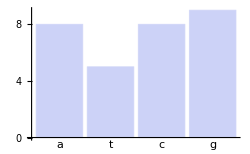

-Graphics-

a | g | c | c | g | a | c | c | c | g | c | t | a | a | t | a | g | g | a | g | t | t | g | g | a | g | t | c | a | c
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
t | c | g | g | c | t | g | g | g | c | g | a | t | t | a | t | c | c | t | c | a | a | c | c | t | c | a | g | t | g
t | a | g | t | c | t | a | c | t | c | c | g | c | t | t | c | a | c | g | a | c | a | g | a | a | t | t | t | a | a
| | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | | |
a | t | c | a | g | a | t | g | a | g | g | c | g | a | a | g | t | g | c | t | g | t | c | t | t | a | a | a | t | t

SRPANRSWSH

_STPLHDRI_

```mathematica
bases={"a","c","g","u"};
randomRNA[n_Integer]:=StringJoin[Table[bases[[Random[Integer,{1,4}]]],{n}]]
RNATable=Table[RNAsequence[i]=randomRNA[30],{i,1,2}]
DNATable=StringReplace[RNATable,{"u"->"t"}]

numOfOcc[sequence_String,base_String]:=Length[Select[Characters[sequence],(#==base)&]];
BarChart[Map[numOfOcc[DNATable[[1]],#]&,{"a","t","c","g"}],ChartLabels->{"a","t","c","g"},ImageSize->250]
PieChart[Map[numOfOcc[DNATable[[2]],#]&,{"a","t","c","g"}],ChartLabels->{"a","t","c","g"},ImageSize->250]

DNASplit1=StringSplit[DNATable[[1]],""];
DNASplit2=StringSplit[DNATable[[2]],""];
cDNASplit1=StringSplit[StringReplace[DNATable[[1]],{"a"->"t","t"->"a","c"->"g","g"->"c"}],""];
cDNASplit2=StringSplit[StringReplace[DNATable[[2]],{"a"->"t","t"->"a","c"->"g","g"->"c"}],""];
sub1=GridBox[{DNASplit1, Table["|", {Length[DNASplit1]}],cDNASplit1}, GridBaseline -> Bottom];
sub2=GridBox[{DNASplit2, Table["|", {Length[DNASplit2]}],cDNASplit2}, GridBaseline -> Bottom];
DisplayForm[FrameBox[GridBox[{{sub1},{sub2}},RowLines -> True]]]

CodonRules={"tca"->"S","tcc"->"S","tcg"->"S","tct"->"S","ttc"->"F",   "ttt"->"F","tta"->"L","ttg"->"L","tac"->"Y","tat"->"Y","taa"->"_","tag"->"_","tgc"->"C","tgt"->"C","tga"->"_","tgg"->"W","cta"->"L","ctc"->"L","ctg"->"L","ctt"->"L","cca"->"P","ccc"->"P","ccg"->"P","cct"->"P","cac"->"H","cat"->"H","caa"->"Q","cag"->"Q","cga"->"R","cgc"->"R","cgg"->"R","cgt"->"R","ata"->"I","att"->"I","atc"->"I","atg"->"M","aca"->"T","acc"->"T","acg"->"T","act"->"T","aac"->"N","aat"->"N","aaa"->"K","aag"->"K","agc"->"S","agt"->"S","aga"->"R","agg"->"R","gta"->"V","gtc"->"V","gtg"->"V","gtt"->"V","gca"->"A","gcc"->"A","gcg"->"A","gct"->"A","gac"->"D","gat"->"D","gaa"->"E","gag"->"E","gga"->"G","ggc"->"G","ggg"->"G","ggt"->"G"};
StringJoin[Partition[Characters[DNATable[[1]]],3]/.{x_,y_,z_}:>StringJoin[x,y,z]/.CodonRules]
StringJoin[Partition[Characters[DNATable[[2]]],3]/.{x_,y_,z_}:>StringJoin[x,y,z]/.CodonRules]
```

### Exercise 3: Reading and analyzing GenBank data file

Read data file from GenBank for  Saccharomyces cerevisiae TCP1-beta gene (The nucleotide ID for  file is U49845)
and extract its gene sequence.  Show frequency distribution of bases using both PieChart and BarChart. Find all the positions of pattern "ctcc" in the sequence, calculate the nummber of occurences and then highlight them. (See the examples in Advanced Documentation: String Patterns to find out how to highlight patterns)

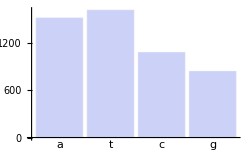

-Graphics-

{{5,8},{23,26},{454,457},{470,473},{489,492},{735,738},{1333,1336},{1573,1576},{1643,1646},{1718,1721},{1784,1787},{2066,2069},{2123,2126},{2146,2149},{2602,2605},{2860,2863},{2965,2968},{3350,3353},{3540,3543},{3556,3559},{3651,3654},{4488,4491},{4863,4866},{4965,4968}}

24

gatcctccatatacaacggtatctccacctcaggtttagatctcaacaacggaaccattgccgacatgagacagttaggtatcgtcgagagttacaagctaaaacgagcagtagtcagctctgcatctgaagccgctgaagttctactaagggtggataacatcatccgtgcaagaccaagaaccgccaatagacaacatatgtaacatatttaggatatacctcgaaaataataaaccgccacactgtcattattataattagaaacagaacgcaaaaattatccactatataattcaaagacgcgaaaaaaaaagaacaacgcgtcatagaacttttggcaattcgcgtcacaaataaattttggcaacttatgtttcctcttcgagcagtactcgagccctgtctcaagaatgtaataatacccatcgtaggtatggttaaagatagcatctccacaacctcaaagctccttgccgagagtcgccctcctttgtcgagtaattttcacttttcatatgagaacttattttcttattctttactctcacatcctgtagtgattgacactgcaacagccaccatcactagaagaacagaacaattacttaatagaaaaattatatcttcctcgaaacgatttcctgcttccaacatctacgtatatcaagaagcattcacttaccatgacacagcttcagatttcattattgctgacagctactatatcactactccatctagtagtggccacgccctatgaggcatatcctatcggaaaacaataccccccagtggcaagagtcaatgaatcgtttacatttcaaatttccaatgatacctataaatcgtctgtagacaagacagctcaaataacatacaattgcttcgacttaccgagctggctttcgtttgactctagttctagaacgttctcaggtgaaccttcttctgacttactatctgatgcgaacaccacgttgtatttcaatgtaatactcgagggtacggactctgccgacagcacgtctttgaacaatacataccaatttgttgttacaaaccgtccatccatctcgctatcgtcagatttcaatctattggcgttgttaaaaaactatggttatactaacggcaaaaacgctctgaaactagatcctaatgaagtcttcaacgtgacttttgaccgttcaatgttcactaacgaagaatccattgtgtcgtattacggacgttctcagttgtataatgcgccgttacccaattggctgttcttcgattctggcgagttgaagtttactgggacggcaccggtgataaactcggcgattgctccagaaacaagctacagttttgtcatcatcgctacagacattgaaggattttctgccgttgaggtagaattcgaattagtcatcggggctcaccagttaactacctctattcaaaatagtttgataatcaacgttactgacacaggtaacgtttcatatgacttacctctaaactatgtttatctcgatgacgatcctatttcttctgataaattgggttctataaacttattggatgctccagactgggtggcattagataatgctaccatttccgggtctgtcccagatgaattactcggtaagaactccaatcctgccaatttttctgtgtccatttatgatacttatggtgatgtgatttatttcaacttcgaagttgtctccacaacggatttgtttgccattagttctcttcccaatattaacgctacaaggggtgaatggttctcctactattttttgccttctcagtttacagactacgtgaatacaaacgtttcattagagtttactaattcaagccaagaccatgactgggtgaaattccaatcatctaatttaacattagctggagaagtgcccaagaatttcgacaagctttcattaggtttgaaagcgaaccaaggttcacaatctcaagagctatattttaacatcattggcatggattcaaagataactcactcaaaccacagtgcgaatgcaacgtccacaagaagttctcaccactccacctcaacaagttcttacacatcttctacttacactgcaaaaatttcttctacctccgctgctgctacttcttctgctccagcagcgctgccagcagccaataaaacttcatctcacaataaaaaagcagtagcaattgcgtgcggtgttgctatcccattaggcgttatcctagtagctctcatttgcttcctaatattctggagacgcagaagggaaaatccagacgatgaaaacttaccgcatgctattagtggacctgatttgaataatcctgcaaataaaccaaatcaagaaaacgctacacctttgaacaacccctttgatgatgatgcttcctcgtacgatgatacttcaatagcaagaagattggctgctttgaacactttgaaattggataaccactctgccactgaatctgatatttccagcgtggatgaaaagagagattctctatcaggtatgaatacatacaatgatcagttccaatcccaaagtaaagaagaattattagcaaaacccccagtacagcctccagagagcccgttctttgacccacagaataggtcttcttctgtgtatatggatagtgaaccagcagtaaataaatcctggcgatatactggcaacctgtcaccagtctctgatattgtcagagacagttacggatcacaaaaaactgttgatacagaaaaacttttcgatttagaagcaccagagaaggaaaaacgtacgtcaagggatgtcactatgtcttcactggacccttggaacagcaatattagcccttctcccgtaagaaaatcagtaacaccatcaccatataacgtaacgaagcatcgtaaccgccacttacaaaatattcaagactctcaaagcggtaaaaacggaatcactcccacaacaatgtcaacttcatcttctgacgattttgttccggttaaagatggtgaaaatttttgctgggtccatagcatggaaccagacagaagaccaagtaagaaaaggttagtagatttttcaaataagagtaatgtcaatgttggtcaagttaaggacattcacggacgcatcccagaaatgctgtgattatacgcaacgatattttgcttaattttattttcctgttttattttttattagtggtttacagataccctatattttatttagtttttatacttagagacatttaattttaattccattcttcaaatttcatttttgcacttaaaacaaagatccaaaaatgctctcgccctcttcatattgagaatacactccattcaaaattttgtcgtcaccgctgattaatttttcactaaactgatgaataatcaaaggccccacgtcagaaccgactaaagaagtgagttttattttaggaggttgaaaaccattattgtctggtaaattttcatcttcttgacatttaacccagtttgaatccctttcaatttctgctttttcctccaaactatcgaccctcctgtttctgtccaacttatgtcctagttccaattcgatcgcattaataactgcttcaaatgttattgtgtcatcgttgactttaggtaatttctccaaatgcataatcaaactatttaaggaagatcggaattcgtcgaacacttcagtttccgtaatgatctgatcgtctttatccacatgttgtaattcactaaaatctaaaacgtatttttcaatgcataaatcgttctttttattaataatgcagatggaaaatctgtaaacgtgcgttaatttagaaagaacatccagtataagttcttctatatagtcaattaaagcaggatgcctattaatgggaacgaactgcggcaagttgaatgactggtaagtagtgtagtcgaatgactgaggtgggtatacatttctataaaataaaatcaaattaatgtagcattttaagtataccctcagccacttctctacccatctattcataaagctgacgcaacgattactattttttttttcttcttggatctcagtcgtcgcaaaaacgtataccttctttttccgaccttttttttagctttctggaaaagtttatattagttaaacagggtctagtcttagtgtgaaagctagtggtttcgattgactgatattaagaaagtggaaattaaattagtagtgtagacgtatatgcatatgtatttctcgcctgtttatgtttctacgtacttttgatttatagcaaggggaaaagaaatacatactattttttggtaaaggtgaaagcataatgtaaaagctagaataaaatggacgaaataaagagaggcttagttcatcttttttccaaaaagcacccaatgataataactaaaatgaaaaggatttgccatctgtcagcaacatcagttgtgtgagcaataataaaatcatcacctccgttgcctttagcgcgtttgtcgtttgtatcttccgtaattttagtcttatcaatgggaatcataaattttccaatgaattagcaatttcgtccaattctttttgagcttcttcatatttgctttggaattcttcgcacttcttttcccattcatctctttcttcttccaaagcaacgatccttctacccatttgctcagagttcaaatcggcctctttcagtttatccattgcttccttcagtttggcttcactgtcttctagctgttgttctagatcctggtttttcttggtgtagttctcattattagatctcaagttattggagtcttcagccaattgctttgtatcagacaattgactctctaacttctccacttcactgtcgagttgctcgtttttagcggacaaagatttaatctcgttttctttttcagtgttagattgctctaattctttgagctgttctctcagctcctcatatttttcttgccatgactcagattctaattttaagctattcaatttctctttgatc

```mathematica
Module[{myGenBankfile,OriginRowNumber,DNAsequence,s,proteinseqString,proteinSeqStart,proteinSeqEnd,proteinSeq},
myGenBankfile=ReadList["/home/jhofman/Desktop/CompBio/lab2/U49845.txt",Word, WordSeparators->{"\r"}];
OriginRowNumber=First[Flatten[Position[myGenBankfile,x_String/;x==First[Select[myGenBankfile,StringMatchQ[#,"ORIGIN*"]&]]]]];
DNAseqence=Table[myGenBankfile[[i]],{i,OriginRowNumber+1,Length[myGenBankfile]}];
For[DNAseqString="";i=1,i<Length[DNAseqence]+1,s=StringToStream[DNAseqence[[i]]];DNAseqString=DNAseqString<>StringJoin[Drop[ReadList[s,Word,RecordSeparators->{" "}],1]];i++];
DNAseqString];

numOfOcc[sequence_String,base_String]:=Length[Select[Characters[sequence],(#==base)&]];
BarChart[Map[numOfOcc[DNAseqString,#]&,{"a","t","c","g"}],ChartLabels->{"a","t","c","g"},ImageSize->250]
PieChart[Map[numOfOcc[DNAseqString,#]&,{"a","t","c","g"}],ChartLabels->{"a","t","c","g"},ImageSize->250]

StringPosition[DNAseqString,"ctcc"]
Length[StringPosition[DNAseqString,"ctcc"]]

StringReplace[DNAseqString,x:("ctcc"):>"\!\(\*StyleBox[\""<>x<>"\",FontColor->RGBColor[1,0,0],FontSize->18,FontWeight->\"Bold\"]\)"]
```

### Exercise 4: Sickle Cell Anemia Gene (optional)

Now let's look at a real case. Sickle cell anemia (For a detailed introduction, please see http://www.ornl.gov/sci/techresources/Human_Genome/posters/chromosome/hbb.shtml) is most commonly caused by a single mutation in the hemoglobin gene sequence resulting a variant Hb S.  In this variant, the hydrophobic amino acid valine takes the place of hydrophilic glutamic acid at the sixth amino acid position of the HBB polypeptide chain. Now your task is to search out the HBB gene (nucleotide ID : 28302128) in GenBank database and try to get a text file about its mRNA. Extract out its gene sequence and find out the nucleotide position where single mutation will happen in the case of sickle blood cell , mutate it and label it as red. Use condon rules to translate the HBB sequence (without mutation) into its corresponding  sequence of amino acids and compare it with the real translation sequence which you can extract from the data text file, explain why there exists very large difference.

```mathematica
Module[{OriginRowNumber,DNAsequence,s,proteinseqString,proteinSeqStart,proteinSeqEnd,proteinSeq},
myGenBankfile=ReadList["/home/jhofman/Desktop/CompBio/lab2/28302128.txt",Word, WordSeparators->{"\r"}];
OriginRowNumber=First[Flatten[Position[myGenBankfile,x_String/;x==First[Select[myGenBankfile,StringMatchQ[#,"ORIGIN*"]&]]]]];
DNAseqence=Table[myGenBankfile[[i]],{i,OriginRowNumber+1,Length[myGenBankfile]}];
For[DNAseqString="";i=1,i<Length[DNAseqence]+1,s=StringToStream[DNAseqence[[i]]];DNAseqString=DNAseqString<>StringJoin[Drop[ReadList[s,Word,RecordSeparators->{" "}],1]];i++];
DNAseqString];
DNAseqString

position=First[StringPosition[DNAseqString,"ctgactcctgaggagaagtct"]][[1]]
anemia =StringReplace[DNAseqString,"ctgactcctgaggagaagtct"->"ctgactcctgtggagaagtct"]

CodonRules={"tca"->"S","tcc"->"S","tcg"->"S","tct"->"S","ttc"->"F",   "ttt"->"F","tta"->"L","ttg"->"L","tac"->"Y","tat"->"Y","taa"->"_","tag"->"_","tgc"->"C","tgt"->"C","tga"->"_","tgg"->"W","cta"->"L","ctc"->"L","ctg"->"L","ctt"->"L","cca"->"P","ccc"->"P","ccg"->"P","cct"->"P","cac"->"H","cat"->"H","caa"->"Q","cag"->"Q","cga"->"R","cgc"->"R","cgg"->"R","cgt"->"R","ata"->"I","att"->"I","atc"->"I","atg"->"M","aca"->"T","acc"->"T","acg"->"T","act"->"T","aac"->"N","aat"->"N","aaa"->"K","aag"->"K","agc"->"S","agt"->"S","aga"->"R","agg"->"R","gta"->"V","gtc"->"V","gtg"->"V","gtt"->"V","gca"->"A","gcc"->"A","gcg"->"A","gct"->"A","gac"->"D","gat"->"D","gaa"->"E","gag"->"E","gga"->"G","ggc"->"G","ggg"->"G","ggt"->"G"};
StringJoin[Partition[Characters[DNAseqString],3]/.{x_,y_,z_}:>StringJoin[x,y,z]/.CodonRules]

pat2=First[Select[myGenBankfile,StringMatchQ[#,"*translation*"]&]];
pat3=First[Select[myGenBankfile,StringMatchQ[#,"*misc_feature    54..56*"]&]];
proteinSeqStart=First[Flatten[Position[myGenBankfile,x_String/;x==pat2]]];
proteinSeqEnd=First[Flatten[Position[myGenBankfile,x_String/;x==pat3]]]-1;
proteinSeq=Table[myGenBankfile[[i]],{i,proteinSeqStart,proteinSeqEnd}];
StringReplace[StringJoin[proteinSeq],{"\""->""," "->"","/translation="->""}]
```

acatttgcttctgacacaactgtgttcactagcaacctcaaacagacaccatggtgcatctgactcctgaggagaagtctgccgttactgccctgtggggcaaggtgaacgtggatgaagttggtggtgaggccctgggcaggctgctggtggtctacccttggacccagaggttctttgagtcctttggggatctgtccactcctgatgctgttatgggcaaccctaaggtgaaggctcatggcaagaaagtgctcggtgcctttagtgatggcctggctcacctggacaacctcaagggcacctttgccacactgagtgagctgcactgtgacaagctgcacgtggatcctgagaacttcaggctcctgggcaacgtgctggtctgtgtgctggcccatcactttggcaaagaattcaccccaccagtgcaggctgcctatcagaaagtggtggctggtgtggctaatgccctggcccacaagtatcactaagctcgctttcttgctgtccaatttctattaaaggttcctttgttccctaagtccaactactaaactgggggatattatgaagggccttgagcatctggattctgcctaataaaaaacatttattttcattgc

60

acatttgcttctgacacaactgtgttcactagcaacctcaaacagacaccatggtgcatctgactcctgtggagaagtctgccgttactgccctgtggggcaaggtgaacgtggatgaagttggtggtgaggccctgggcaggctgctggtggtctacccttggacccagaggttctttgagtcctttggggatctgtccactcctgatgctgttatgggcaaccctaaggtgaaggctcatggcaagaaagtgctcggtgcctttagtgatggcctggctcacctggacaacctcaagggcacctttgccacactgagtgagctgcactgtgacaagctgcacgtggatcctgagaacttcaggctcctgggcaacgtgctggtctgtgtgctggcccatcactttggcaaagaattcaccccaccagtgcaggctgcctatcagaaagtggtggctggtgtggctaatgccctggcccacaagtatcactaagctcgctttcttgctgtccaatttctattaaaggttcctttgttccctaagtccaactactaaactgggggatattatgaagggccttgagcatctggattctgcctaataaaaaacatttattttcattgc

TFASDTTVFTSNLKQTPWCI_LLRRSLPLLPCGAR_TWMKLVVRPWAGCWWSTLGPRGSLSPLGICPLLMLLWATLR_RLMARKCSVPLVMAWLTWTTSRAPLPH_VSCTVTSCTWILRTSGSWATCWSVCWPITLAKNSPHQCRLPIRKWWLVWLMPWPTSITKLAFLLSNFY_RFLCSLSPTTKLGDIMKGLEHLDSA__KTFIFI

MVHLTPEEKSAVTALWGKVNVDEVGGEALGRLLVVYPWTQRFFESFGDLSTPDAVMGNPKVKAHGKKVLGAFSDGLAHLDNLKGTFATLSELHCDKLHVDPENFRLLGNVLVCVLAHHFGKEFTPPVQAAYQKVVAGVANALAHKYH